```mathematica
ClearAll["Global`*"]
```

```mathematica
(* set your home directory *)
SetDirectory[NotebookDirectory[]];
```

## mesh

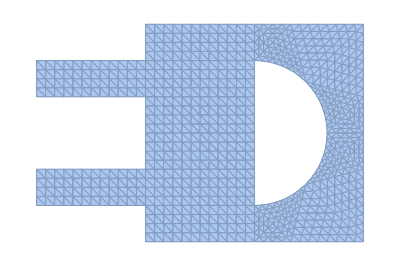

```mathematica
nodes=Import["n.dat","Table"];
nodeCount=Length@nodes;
triangles=Import["t.dat","Table"]+1;
𝒦=MeshRegion[nodes,Triangle/@triangles]
HighlightMesh[𝒦,0,MeshCellLabel->{0->"Index"}];
```

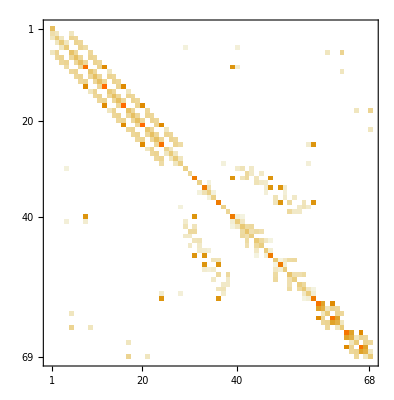

```mathematica
matrix=Import["m.dat","Table"];
MatrixPlot@matrix
```

#### bndry

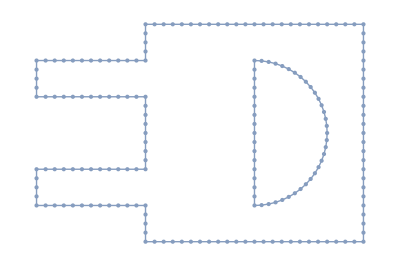

```mathematica
bndryEdges=Import["bndry.dat","Table","FieldSeparators"-> {"\n"},"LineSeparators"-> {"\n\n"}]+1;
𝒮=MeshRegion[nodes,Line/@bndryEdges]
HighlightMesh[𝒮,0,MeshCellLabel->{1->"Index"}];
```

## soln

```mathematica
time=Import["time.dat","List"];
timeCount=Length@time;
ξ=Chop@Import["xi.dat","Table","FieldSeparators"-> {"\n"},"LineSeparators"-> {"\n\n"}];
Do[Subscript[u, m]=Interpolation[Table[{nodes[[i]],ξ[[m,i]]},{i,nodeCount}],InterpolationOrder->1],{m,timeCount}]
```

```mathematica
waveFrames=Table[Plot3D[Subscript[u, m][x,y],{x,y}∈𝒦,PlotLabel->"t = "<>ToString[time[[m]]], PlotRange->{-.05,.05},Axes->False,Boxed->False,Mesh->None],{m,timeCount}];
```

```mathematica
Manipulate[waveFrames[[m]],{{m,1,"time frame"},1,timeCount,1}]
```